```mathematica
TransformedDistribution[
σScreen*σScreen,
{
σScreen\[Distributed]NormalDistribution[μσScreen,σσScreen],
σOff\[Distributed]NormalDistribution[μσOff,σσOff]
}
]
```

TransformedDistribution[x1^2,{x1}\[Distributed]TransformedDistribution[{x},x\[Distributed]NormalDistribution[μσScreen,σσScreen]]]

```mathematica
data =ImportString[" -1, 0.001463870524947474
 0, 0.00047288595738029726
 1, 0.0015314520018408838
 -1, 0.0015990216946601093
 0, 0.000488025717938945
 1, 0.001702715083358308
 -1, 0.0015840824570475
 0, 0.0004415050596621244
 1, 0.0016658283063040557
 -1, 0.001981712299712555
 0, 0.0005222530245381091
 1, 0.0017697200301395532
 -1, 0.0014666899862966108
 0, 0.00045537560463279814
 1, 0.0018473205035243142
 -1, 0.0013760208707809464
 0, 0.0004859513693057428
 1, 0.00173260856250911
 -1, 0.002051708016449268
 0, 0.0004954909340642246
 1, 0.0010361132520943922
 -1, 0.0019271012186153709
 0, 0.0004533206230957517
 1, 0.001938710604969935
 -1, 0.0017277901577373476
 0, 0.00048823842599653476
 1, 0.0015677181790459992
 -1, 0.0017144755734529442
 0, 0.0004857739148630236
 1, 0.001810528644912713
","CSV"];

(*data=data[[1;;6]];*)

(*Convert to microns*)
data[[All,2]]*=10^6;
```

```mathematica
exprσScreen = √(σOff^2+(κ V σz)^2)/.κ->(1/0.073);
nlm = NonlinearModelFit[
data,
exprσScreen,
{σOff,σz},
V
]
```

FittedModel[…]

```mathematica
aroundData = Around[#[[All,2]]]&/@GroupBy[data,First]
```

<|-1→1689.234.,0→479.24.,1→1660.251.|>

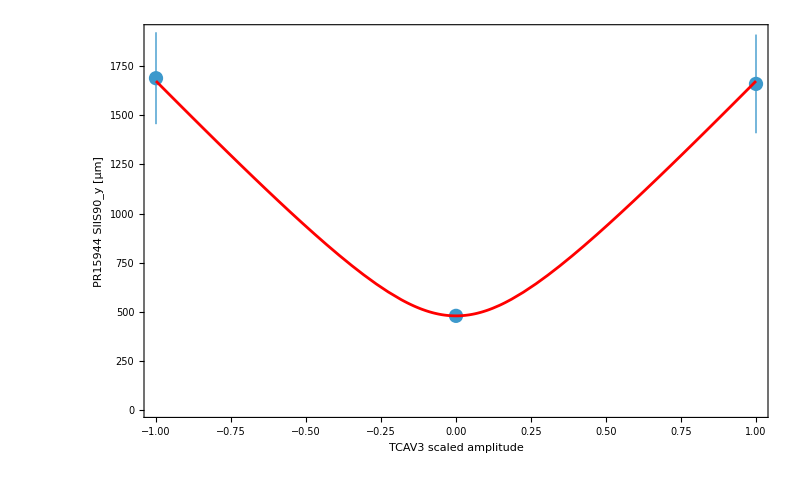

```mathematica
Show[
ListPlot[aroundData,ImageSize->800,Frame->True,LabelStyle->20,FrameLabel->{"TCAV3 scaled amplitude", "PR15944 SIIS90_y [μm]"}],
Plot[nlm["BestFit"],{V,-1,1},PlotStyle->Red]
]
```

```mathematica
nlm["ParameterEstimates"]
```

## Attempt directly inverting

```mathematica
Solve[σScreen == √(σOff^2+(κ V σz)^2),σz]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{σz→-(√(-σOff^2+σScreen^2))/(V κ)},{σz→(√(-σOff^2+σScreen^2))/(V κ)}}

```mathematica
(√(-σOff^2+σScreen^2))/(V κ)
```

```mathematica
TransformedDistribution[
(√(-σOff^2+σScreen^2))/(V κ),
{
σScreen\[Distributed]NormalDistribution[μσScreen,σσScreen],
σOff\[Distributed]NormalDistribution[μσOff,σσOff]
}
]
```

TransformedDistribution[(√(x1^2-x2^2))/(V κ),{x1\[Distributed]NormalDistribution[μσScreen,σσScreen],x2\[Distributed]NormalDistribution[μσOff,σσOff]}]

From “2025-01-28 Analytic uncertainty propagation - compare to Around.nb”

```mathematica
powerAround[a_,n_]:={a[[1]]^n, Abs[a[[1]]^n * n * a[[2]] / a[[1]] ]}
plusAround[a_,b_]:={a[[1]]+b[[1]],√(a[[2]]^2+b[[2]]^2)}
```

```mathematica
powerAround[plusAround[powerAround[{μσScreen,σσScreen},2],-powerAround[{μσOff,σσOff},2]],1/2]/(V κ)
```

{(√(-μσOff^2+μσScreen^2))/(V κ),Abs[(√(4 Abs[μσOff σσOff]^2+4 Abs[μσScreen σσScreen]^2))/(√(-μσOff^2+μσScreen^2))]/(2 V κ)}

## Get the standard errors for these quantities and propagate

### First get σOff; it’s equal to the screen value with V = 0

```mathematica
offMeasurements = Select[data,#[[1]]==0&][[All,2]]
Mean[offMeasurements]
StandardDeviation[offMeasurements]
StandardDeviation[offMeasurements]/Sqrt[Length[offMeasurements]]
```

{472.886,488.026,441.505,522.253,455.376,485.951,495.491,453.321,488.238,485.774}

478.882

23.7216

7.50144

So μσOff = 478.882 with standard error 7.50144

### Now, for each measurement, estimate σz

```mathematica
(√(-(Around[478.882,7.50144]^2+σScreen^2))/(V κ)
```

{1463.87,1531.45,1599.02,1702.72,1584.08,1665.83,1981.71,1769.72,1466.69,1847.32,1376.02,1732.61,2051.71,1036.11,1927.1,1938.71,1727.79,1567.72,1714.48,1810.53}

No, I decided I don’t like this

### Directly propagating standard errors

```mathematica
offMeasurements = Select[data,#[[1]]==0&][[All,2]];
onMeasurements = Select[data,#[[1]]!=0&][[All,2]];
```

```mathematica
aroundWithStandardError[pop_]:=Around[Mean[pop],StandardDeviation[pop]/√Length[pop]]
```

```mathematica
Abs[(√(-σOff^2+σScreen^2))/(V κ)]/.{σOff->aroundWithStandardError[offMeasurements],σScreen->aroundWithStandardError[onMeasurements],V->1,κ->(1/0.073)}
```

117.4.

This approach seems reasonable, but doesn’t accommodate varying V values

## Monte Carlo error propagation

The general solution for σz is |(√(-σOff^2+σScreen^2))/(V κ)|

Although my data only has |V| = 1, the following Monte Carlo method would be general if, e.g. V was varying

```mathematica
offMeasurements = Select[data,#[[1]]==0&][[All,2]]
onMeasurements = Select[data,#[[1]]!=0&][[All,2]]
```

{472.886,488.026,441.505,522.253,455.376,485.951,495.491,453.321,488.238,485.774}

{1463.87,1531.45,1599.02,1702.72,1584.08,1665.83,1981.71,1769.72,1466.69,1847.32,1376.02,1732.61,2051.71,1036.11,1927.1,1938.71,1727.79,1567.72,1714.48,1810.53}

My concern with this is doing the appropriate number of samples... too few, and I’ll overestimate the standard error, too many and I’ll be duplicating virtual measurements since I have a finite number of “real” numbers to sample from

I’ll try two cases: number of trials equal to the number of offMeasurements and number of trials equal to the onMeasurements

### 10 trials

```mathematica
results = Table[
Abs[(√(-σOff^2+σScreen^2))/(V κ)]/.{σOff->RandomChoice[offMeasurements],σScreen->RandomChoice[onMeasurements],V->1,κ->(1/0.073)},
10
];
Mean[results]
StandardDeviation[results]
StandardDeviation[results]/Sqrt[Length[results]]
```

116.811

14.6866

4.64431

### 20 trials

```mathematica
results = Table[
Abs[(√(-σOff^2+σScreen^2))/(V κ)]/.{σOff->RandomChoice[offMeasurements],σScreen->RandomChoice[onMeasurements],V->1,κ->(1/0.073)},
20
];
Mean[results]
StandardDeviation[results]
StandardDeviation[results]/Sqrt[Length[results]]
```

117.499

17.9118

4.00521

### 20*10 trials

```mathematica
results = Table[
Abs[(√(-σOff^2+σScreen^2))/(V κ)]/.{σOff->RandomChoice[offMeasurements],σScreen->RandomChoice[onMeasurements],V->1,κ->(1/0.073)},
200
];
Mean[results]
StandardDeviation[results]
StandardDeviation[results]/Sqrt[Length[results]]
```

116.793

19.5353

1.38136

## Toy model - sanity check

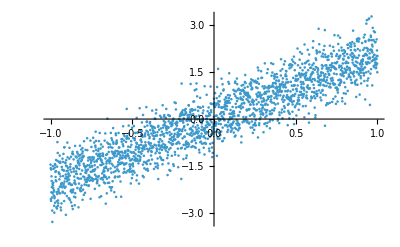

```mathematica
fakeData = Table[{x, 2.1 x + 0.5RandomVariate[NormalDistribution[0,1],1][[1]]},{x,-1,1,0.001}];

(*Randomize order*)
fakeData=RandomSample[fakeData];


ListPlot[fakeData]
```

```mathematica
nlm = NonlinearModelFit[
fakeData[[1;;50]],
m x + b,
{m,b},
x
];
nlm["ParameterEstimates"]
{Mean[#],#[[2]]-#[[1]]}&/@(#["ConfidenceInterval"]&/@Normal[nlm["ParameterEstimates"]])//TableForm
```

2.11639 | 0.468663
-0.0278048 | 0.270469

```mathematica
nlm = NonlinearModelFit[
fakeData[[1;;200]],
m x + b,
{m,b},
x
];
nlm["ParameterEstimates"]
{Mean[#],#[[2]]-#[[1]]}&/@(#["ConfidenceInterval"]&/@Normal[nlm["ParameterEstimates"]])//TableForm
```

1.98376 | 0.238544
-0.0210837 | 0.1415

```mathematica
nlm = NonlinearModelFit[
fakeData[[1;;400]],
m x + b,
{m,b},
x
];
nlm["ParameterEstimates"]
{Mean[#],#[[2]]-#[[1]]}&/@(#["ConfidenceInterval"]&/@Normal[nlm["ParameterEstimates"]])//TableForm
```

2.01628 | 0.166988
0.0284623 | 0.0965651

```mathematica
nlm = NonlinearModelFit[
fakeData[[1;;800]],
m x + b,
{m,b},
x
];
nlm["ParameterEstimates"]
{Mean[#],#[[2]]-#[[1]]}&/@(#["ConfidenceInterval"]&/@Normal[nlm["ParameterEstimates"]])//TableForm
```

General::munfl: Exp[-757.006] is too small to represent as a normalized machine number; precision may be lost.

2.09068 | 0.122675
0.034814 | 0.0709663

General::munfl: Exp[-757.006] is too small to represent as a normalized machine number; precision may be lost.

2.0910.031

```mathematica
summaryResults = Table[
nlm = NonlinearModelFit[
fakeData[[1;;n]],
m x + b,
{m,b},
x
];


{n,
Around[#BestFitValue,#StandardError]&@Normal[nlm["ParameterEstimates"]][[1]],  
Normal[nlm["ParameterEstimates"]][[1]]["ConfidenceInterval"][[1]],
 Normal[nlm["ParameterEstimates"]][[1]]["ConfidenceInterval"][[2]]
},
{n,3,Length[fakeData],5}
];
```

General::munfl: Exp[-711.505] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

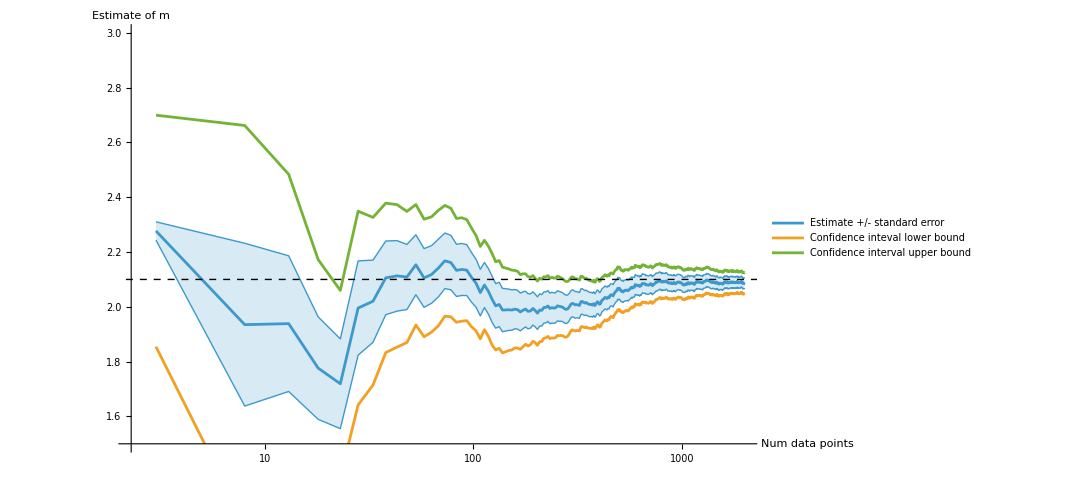

```mathematica
Show[
ListLogLinearPlot[{
summaryResults[[All,{1,2}]],
summaryResults[[All,{1,3}]],
summaryResults[[All,{1,4}]]
},
IntervalMarkers->"Bands",
ImageSize->800,
Joined->True,
PlotRange->{1.5,3},
AxesLabel->{"Num data points","Estimate of m"},
PlotLegends->{"Estimate +/- standard error","Confidence inteval lower bound","Confidence interval upper bound"}
],
Graphics[
{
Black,
Dashed,
Line[{{0,2.1},{1000,2.1}}]
}
]
]
```

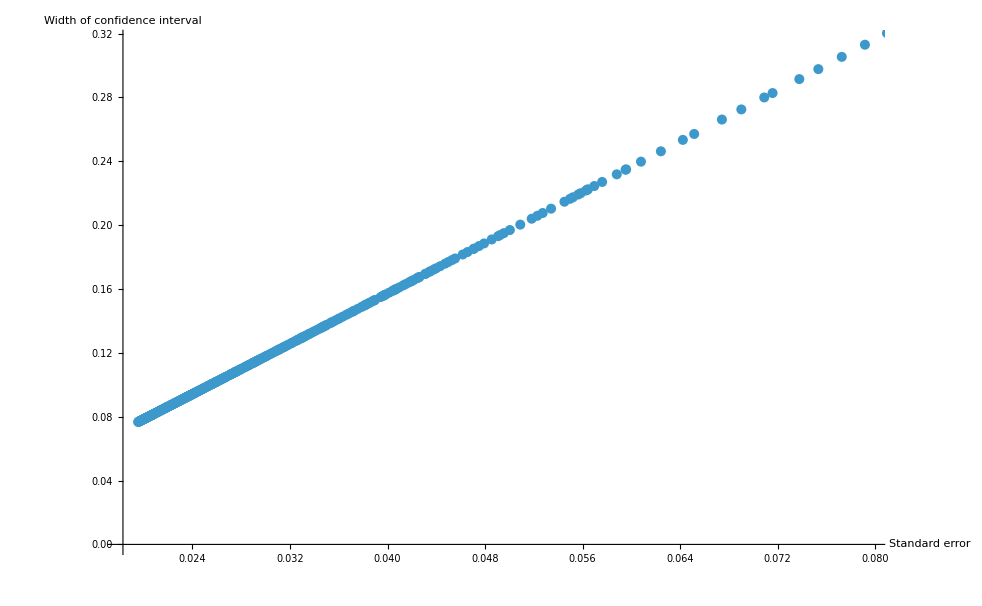

```mathematica
ListPlot[
Transpose[
{
#["Uncertainty"]&/@summaryResults[[All,2]],
#[[4]]-#[[3]]&/@summaryResults
}
],
AxesLabel->{"Standard error","Width of confidence interval"}
]
```

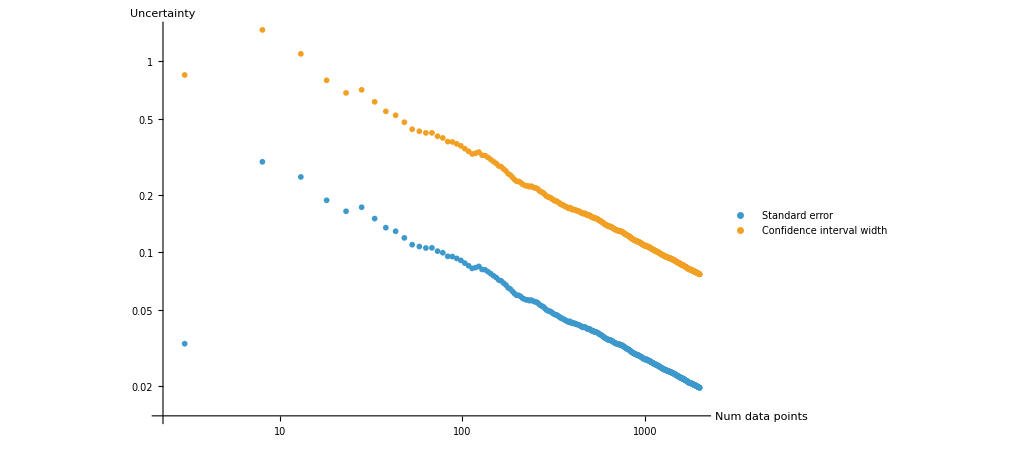

```mathematica
ListLogLogPlot[
{
{#[[1]],#[[2]]["Uncertainty"]}&/@summaryResults,
{#[[1]],#[[4]]-#[[3]]}&/@summaryResults
}
,
AxesLabel->{"Num data points","Uncertainty"},
PlotLegends->{"Standard error","Confidence interval width"}
]
```

## Synthetic experiment

```mathematica
exprσScreen = √(σOff^2+(κ V σz)^2)/.κ->(1/0.073);
```

```mathematica
syntheticμσOff = 100;
syntheticσσOff = 1.1;

syntheticμσz = 150;
syntheticσσz = 2.3;

σV = 0.1;
```

```mathematica
syntheticOffData =Table[
 {0,√(σOff^2+(κ V σz)^2)}/.{κ->(1/0.073),σOff ->RandomVariate[NormalDistribution[syntheticμσOff,syntheticσσOff]],V->0},
10
]
```

{{0,102.172},{0,100.37},{0,100.867},{0,98.6916},{0,100.395},{0,99.2226},{0,101.63},{0,101.768},{0,97.3354},{0,101.446}}

```mathematica
syntheticPlusData =Table[
 {V,√(σOff^2+(κ V σz)^2)}/.{κ->(1/0.073),σOff ->RandomVariate[NormalDistribution[syntheticμσOff,syntheticσσOff]],σz->RandomVariate[NormalDistribution[syntheticμσz,syntheticσσz]],V->RandomVariate[NormalDistribution[1,σV]]},
10
]

syntheticMinusData =Table[
 {V,√(σOff^2+(κ V σz)^2)}/.{κ->(1/0.073),σOff ->RandomVariate[NormalDistribution[syntheticμσOff,syntheticσσOff]],σz->RandomVariate[NormalDistribution[syntheticμσz,syntheticσσz]],V->RandomVariate[NormalDistribution[-1,σV]]},
Length[syntheticPlusData]
]

syntheticOnData = syntheticPlusData~Join~syntheticMinusData;
```

{{1.02989,2063.84},{0.816717,1672.37},{0.957564,1937.15},{1.09091,2273.01},{1.00343,2046.24},{0.892424,1871.15},{0.932474,1917.56},{1.04744,2122.27},{0.978379,1974.65},{0.943408,1913.33}}

{{-0.891542,1805.83},{-0.911916,1842.14},{-0.927042,1921.13},{-0.986121,2020.75},{-0.8225,1706.42},{-0.997704,2056.81},{-0.898263,1795.23},{-1.05692,2196.01},{-0.91516,1850.74},{-1.08428,2227.96}}

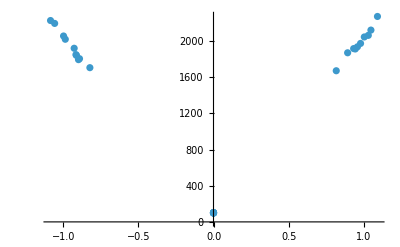

```mathematica
ListPlot[syntheticOffData~Join~syntheticOnData]
```

### Reconstruct - Monte Carlo

Look at each “on” measurement. Use a random “off” measurement to infer the σz

```mathematica
results = Table[
Abs[(√(-σOff^2+σScreen^2))/(V κ)]/.{σOff->RandomChoice[syntheticOffData][[2]],σScreen->row[[2]],V->row[[1]],κ->(1/0.073)},
{row,syntheticOnData }
];

Mean[results]
StandardDeviation[results]
StandardDeviation[results]/Sqrt[Length[results]]
```

149.015

2.027

0.453251

#### Reconstruct; assuming V isn’t known

```mathematica
results = Table[
Abs[(√(-σOff^2+σScreen^2))/(V κ)]/.{σOff->RandomChoice[syntheticOffData][[2]],σScreen->row[[2]],V->1,κ->(1/0.073)},
{row,syntheticOnData }
];

Mean[results]
StandardDeviation[results]
StandardDeviation[results]/Sqrt[Length[results]]
```

142.946

12.1043

2.7066